```mathematica
Quit[]
```

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
FV[a_,μ_]:=ExpandScalarProduct[Pair[Momentum[a],LorentzIndex[μ]]]
```

```mathematica
η[μ_,σ_]:=MetricTensor[μ,σ]
```

```mathematica
<<
```

```mathematica
M2elem[s_,t_,Mχ_,Ma_,f_]:=ExpandScalarProduct[1/(64 f^4)(1/((t-Mχ^2)^2)Tr[(GS[p2]-Mχ).GS[p4].(GS[p3]-GS[p1]+Mχ).GS[p3].(GS[p1]+Mχ).GS[p3].(GS[p3]-GS[p1]+Mχ).GS[p4]]+1/((u-Mχ^2)^2)Tr[(GS[p2]-Mχ).GS[p3].(GS[p4]-GS[p1]+Mχ).GS[p4].(GS[p1]+Mχ).GS[p4].(GS[p4]-GS[p1]+Mχ).GS[p3]]+1/((u-Mχ^2)(t-Mχ^2))Tr[(GS[p2]-Mχ).GS[p4].(GS[p3]-GS[p1]+Mχ).GS[p3].(GS[p1]+Mχ).GS[p4].(GS[p4]-GS[p1]+Mχ).GS[p3]]+1/((u-Mχ^2)(t-Mχ^2))Tr[(GS[p2]-Mχ).GS[p3].(GS[p4]-GS[p1]+Mχ).GS[p4].(GS[p1]+Mχ).GS[p3].(GS[p3]-GS[p1]+Mχ).GS[p4]])]/.Pair[Momentum[p1],Momentum[p1]]->Mχ^2/.Pair[Momentum[p2],Momentum[p2]]->Mχ^2/.Pair[Momentum[p3],Momentum[p3]]->Ma^2/.Pair[Momentum[p4],Momentum[p4]]->Ma^2/.Pair[Momentum[p1],Momentum[p2]]->(s-2 Mχ^2)/2/.Pair[Momentum[p1],Momentum[p3]]->(Ma^2+Mχ^2-t)/2/.Pair[Momentum[p1],Momentum[p4]]->(Ma^2+Mχ^2-u)/2/.Pair[Momentum[p2],Momentum[p3]]->(Ma^2+Mχ^2-u)/2/.Pair[Momentum[p2],Momentum[p4]]->(Ma^2+Mχ^2-t)/2/.Pair[Momentum[p3],Momentum[p4]]->(s-2 Ma^2)/2/.u->2 Mχ^2+2 Ma^2-s-t//Simplify;
```

0

(mchi^2 s (mchi^4-2 mchi^2 t+t (s+t)))/(2 f^4 (mchi^2-t) (mchi^2-s-t))

```mathematica
M = M2elem[s, t, mchi, ma, f] //Simplify
```

(mchi^2 (-4 ma^8 mchi^2+4 ma^6 mchi^2 s-ma^4 s (4 mchi^4+mchi^2 s-4 t^2)+2 ma^2 s (mchi^2-t) (mchi^2 (s-2 t)+2 t (s+t))+s (mchi^2-t) (mchi^6-mchi^4 (s+3 t)+3 mchi^2 t (s+t)-t (s+t)^2)))/(2 f^4 (mchi^2-t)^2 (-2 ma^2-mchi^2+s+t)^2)

```mathematica
Integrate [-M2elem[s,t,mchi,ma,f]/(32*pi*s(s-4*mchi^2)),{t, mchi^2-s/2-(1/2)*(s(s-4*mchi^2))^(1/2), mchi^2-s/2+(1/2)*(s(s-4*mchi^2))^(1/2)}]//InputForm
```

ConditionalExpression[
 -1/64*(mchi^2*((2*ma^4*mchi^2)/(-s + Sqrt[s*(-4*mchi^2 + s)]) + 
     (2*ma^4*mchi^2)/(4*ma^2 - s + Sqrt[s*(-4*mchi^2 + s)]) + 
     (2*ma^4*mchi^2)/(s + Sqrt[s*(-4*mchi^2 + s)]) + 
     (2*ma^4*mchi^2)/(-4*ma^2 + s + Sqrt[s*(-4*mchi^2 + s)]) + 
     (s*(-2*mchi^2 + s + Sqrt[s*(-4*mchi^2 + s)]))/2 + 
     s*(mchi^2 + (-s + Sqrt[s*(-4*mchi^2 + s)])/2) - 
     (mchi^2*(2*ma^4 - 4*ma^2*s + s^2)*(Log[2] - Log[-s - Sqrt[s*(-4*mchi^2 + s)]]))/
      (2*ma^2 - s) - (mchi^2*(2*ma^4 - 4*ma^2*s + s^2)*
       Log[(-4*ma^2 + s - Sqrt[s*(-4*mchi^2 + s)])/2])/(2*ma^2 - s) + 
     (mchi^2*(2*ma^4 - 4*ma^2*s + s^2)*(Log[2] - Log[-s + Sqrt[s*(-4*mchi^2 + s)]]))/
      (2*ma^2 - s) + (mchi^2*(2*ma^4 - 4*ma^2*s + s^2)*
       Log[(-4*ma^2 + s + Sqrt[s*(-4*mchi^2 + s)])/2])/(2*ma^2 - s)))/
   (f^4*pi*s*(-4*mchi^2 + s)), Re[-4*ma^2 + s] >= 0 && Re[s] <= 0 && 
  (NotElement[s/Sqrt[s*(-4*mchi^2 + s)], Reals] || Re[s/Sqrt[s*(-4*mchi^2 + s)]] > 1 || 
   Re[s/Sqrt[s*(-4*mchi^2 + s)]] < -1) && 
  (NotElement[((-4*ma^2 + s)*Sqrt[s*(-4*mchi^2 + s)])/((4*mchi^2 - s)*s), Reals] || 
   Re[((-4*ma^2 + s)*Sqrt[s*(-4*mchi^2 + s)])/((4*mchi^2 - s)*s)] > 1 || 
   Re[((-4*ma^2 + s)*Sqrt[s*(-4*mchi^2 + s)])/((4*mchi^2 - s)*s)] < -1)]

0

ConditionalExpression[1/(64 f^4 pi (4 mchi^2-s))(mchi^2 √(-(s (4 mchi^2-s)))+mchi^4 (-log(-√(s (s-4 mchi^2))-s))+mchi^4 log(s-√(s (s-4 mchi^2)))+mchi^4 log(√(s (s-4 mchi^2))-s)-mchi^4 log(√(s (s-4 mchi^2))+s)), ]

```mathematica
sigma[s_, mchi_,ma_, f_]  := Re[1/64*(mchi^2*((s*(-2*mchi^2+s+Sqrt[s*(-4*mchi^2+s)]))/2+s*(mchi^2+(-s+Sqrt[s*(-4*mchi^2+s)])/2)-(ma^4*mchi^2*(-2*ma^2+Sqrt[s*(-4*mchi^2+s)]))/(mchi^2*s+ma^2*(-s+Sqrt[s*(-4*mchi^2+s)]))+(ma^4*mchi^2*(2*ma^2+Sqrt[s*(-4*mchi^2+s)]))/(-(mchi^2*s)+ma^2*(s+Sqrt[s*(-4*mchi^2+s)]))+(mchi^2*(2*ma^4-4*ma^2*s+s^2)*(Log[-s-Sqrt[s*(-4*mchi^2+s)]]-Log[-4*ma^2+s-Sqrt[s*(-4*mchi^2+s)]]))/(2*ma^2-s)-(mchi^2*(2*ma^4-4*ma^2*s+s^2)*(Log[-s+Sqrt[s*(-4*mchi^2+s)]]-Log[-4*ma^2+s+Sqrt[s*(-4*mchi^2+s)]]))/(2*ma^2-s)))/(f^4*Pi*s*(-4*mchi^2+s))]//N;
```

5.24262×10^-6

4.97359×10^-13

```mathematica
Limit[sigma[4,mχ,0,1],mχ->0]
```

```mathematica
0.
```

0.

```mathematica
average[mchi_, ma_, T_, f_] := NIntegrate[(1/(f^4*8*mchi^4*T*BesselK[2,mchi/T]^2))*sigma[s, mchi, ma, 1]*(s-4*mchi^2)*s^.5*BesselK[1, s^.5/T], {s, 4*mchi^2, Infinity}]/.mchi/T->x/.ma/mchi->y(* note that we've taken f out of the calculation and put it back in later, y is defined like this instead of ma/T because T will be changing later *)
```

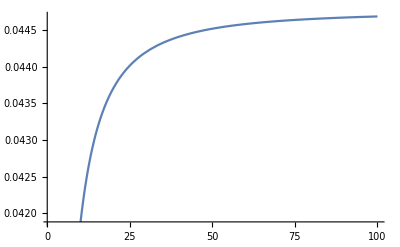

```mathematica
Plot[average[3, 1, x,1],{x,1,100}]
```

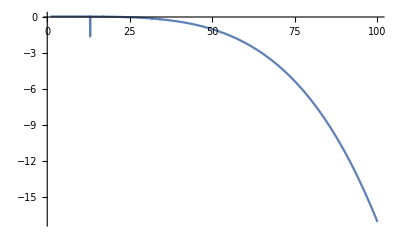

```mathematica
Plot[average[3, x, 10, 1],{x,1,100}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {179.769}. NIntegrate obtained 0.0423268 and 0.000148051 for the integral and error estimates.

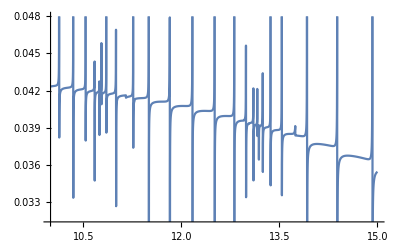

```mathematica
Plot[average[3,x,10,1],{x,10,15}]
```